```mathematica
f[x_]:=x^3-4 x^2-6 x+5
th=10^(-10);
bias=10^3;
xCurrent=3;
xPrev=6;
points={{xPrev,N[f[xPrev]]},{xCurrent,N[f[xCurrent]]}};

While[bias>th,
If[f[xCurrent]-f[xPrev]==0,Print["Division by zero error"];
Break[];];

lim=N[(f[xCurrent]-f[xPrev])/(xCurrent-xPrev)];
xNew=N[xCurrent-f[xCurrent]/lim];
bias=Abs[xNew-xCurrent];
points=Append[points,{xNew,N[f[xNew]]}];
xPrev=xCurrent;
xCurrent=xNew;];

points
```

{{6,41.},{3,-22.},{4.04762,-18.5056},{9.59551,462.628},{4.261,-15.8272},{4.43747,-13.0106},{5.25259,8.04309},{4.94119,-1.66761},{4.99467,-0.15432},{5.00012,0.00351443},{5.,-7.11847×10^-6},{5.,-3.27198×10^-10},{5.,0.}}

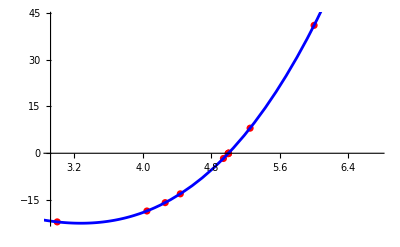

```mathematica
q := Plot[f[x], {x,2, 8}, PlotStyle->Blue]
p := ListPlot[points, PlotStyle->Red]
Show[p,q]
```